## Plots

```mathematica
SetDirectory["/Users/shainen/Dropbox/Research/bhsucon/nb/nb/"];
```

```mathematica
Get["constants.m"]
```

```mathematica
TE=128;
```

```mathematica
QMSz=Import["data/QMAvgSz3","Table"];
```

```mathematica
QMSzold=Import["data/QMAvgSz","Table"];
```

```mathematica
QMwid=Import["data/QMWidSz3","Table"];
```

```mathematica
QM=ListPlot[Table[{times[[1;;TE]],QMSz[[n,1;;TE]]}ᵀ,{n,1,3}],Joined->True];
```

```mathematica
QMold=ListPlot[Table[{times[[1;;TE]],QMSzold[[n,1;;TE]]}ᵀ,{n,1,3}],Joined->True];
```

```mathematica
QMw=ListPlot[Table[{times[[1;;TE]],QMwid[[n,1;;TE]]}ᵀ,{n,1,3}],Joined->True];
```

```mathematica
Get["data/su3S3t200j0.01r1000000.lsta"];
```

```mathematica
TWAsu3=ListPlot[Table[{times[[1;;TE]],2avgspins3[[1;;TE,1,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dashed];
```

```mathematica
TWAsu3w=ListPlot[Table[{times[[1;;TE]],4avgspins3[[1;;TE,2,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted];
```

```mathematica
TWAsu3w8=ListPlot[Table[{times[[1;;TE]],2/3(1-√3 avgspins3[[1;;TE,1,n,8]])-4 avgspins3[[1;;TE,1,n,3]]^2}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dashed];
```

```mathematica
Get["data/su2awS3t200j0.01r100000sp.lst"];
```

```mathematica
Get["data/su2awS3t200j0.01r100000cor.lst"];
```

```mathematica
TWAsu2=ListPlot[Table[{times[[1;;TE]],avgspins2[[1;;TE,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted];
```

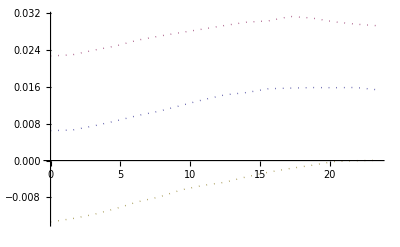

```mathematica
TWAsu2w=ListPlot[Table[{times[[1;;TE]],avgcor2[[1;;TE,n,n,3]]-1/8-avgspins2[[1;;TE,n,3]]^2}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted]
```

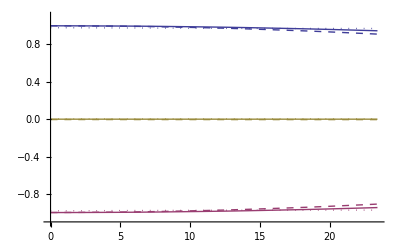

```mathematica
Show[TWAsu3,TWAsu2,QM,PlotRange->{-1.1,1.1},AxesOrigin->{0,-1.1}]
```

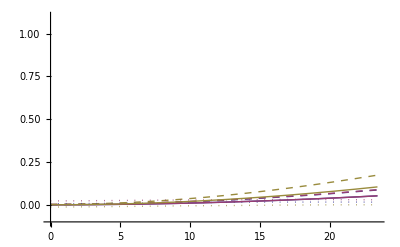

```mathematica
Show[TWAsu3w8,TWAsu2w,QMw,PlotRange->{-0.1,1.1},AxesOrigin->{0,-0.1}]
```

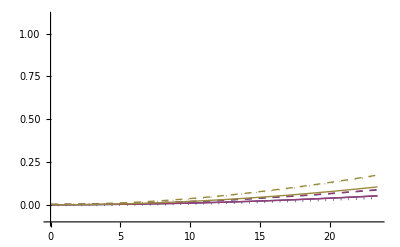

```mathematica
Show[TWAsu3w8,TWAsu3w,QMw,PlotRange->{-0.1,1.1},AxesOrigin->{0,-0.1}]
```